## 6 - ring Hubbard model

6 - Hubbard model ring

#### Basis for the sector with Sz sector (s1,s2)

```mathematica
n = 6;
E0 = 10;
s1 = 3;
s2 = 3;
base =.;
j = 0;
For[i = 0, i < 4^n, i++, vec = IntegerDigits[i, 2, 2 n];
n1 = Total[Take[vec, {1, n}]];
n2 = Total[Take[vec, {n + 1, 2 n}]];
If [n2 == s2 && n1 == s1, 
j++;
base[j] = vec]];
size = j;
```

#### Basis size

```mathematica
size
base[224]
```

400

{1,0,0,1,0,1,0,0,1,1,1,0}

#### Some diagonal operators: double occupancy in site i, Sz in site i, ...

```mathematica
up[x_] := Take[x, {1, n}];
dn[x_] := Take[x, {n + 1, 2 n}];
nn[x_] := Total[up[x] * dn[x]];
norm[x_] := Total[Abs[x]];
diag[i_]:=Table[base[k][[i]] * base[k][[i + n]], {k, 1, size}]
Double[i_] := DiagonalMatrix[
Table[base[k][[i]] * base[k][[i + n]], {k, 1, size}]
];
DoubleSiteAvg := Total[Table[Double[i], {i, 1, n}]]  n;
OpSz[i_] := DiagonalMatrix[Table[base[k][[i]] - base[k][[i + n]], {k, 1, size}]];
OpSzSz[i_, j_] := OpSz[i].OpSz[j];

nn[base[224]]
diag[2]
```

1

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1}

#### Hopping matrix

```mathematica
hop = Join[Table[i + j, {i, 1, n - 1}, {j, 0, 1}],
Table[i - j, {i, 2, n}, {j, 0, 1}], {{n, 1}, {1, n}},
Table[i + j, {i, n + 1, 2 n - 1}, {j, 0, 1}],
Table[i - j, {i, n + 2, 2 n}, {j, 0, 1}], {{2 n, n + 1}, {n + 1, 2 n}}];
Length[hop]
hop
```

24

{{1,2},{2,3},{3,4},{4,5},{5,6},{2,1},{3,2},{4,3},{5,4},{6,5},{6,1},{1,6},{7,8},{8,9},{9,10},{10,11},{11,12},{8,7},{9,8},{10,9},{11,10},{12,11},{12,7},{7,12}}

#### Hopping Hamiltonian in many-body basis

```mathematica
HopTest[x_, y_, cre_, anh_] :=
norm[x - y] == 2 && x[[cre]] == 1 && x[[anh]] == 0 && y[[cre]] == 0 && y[[anh]] == 1;
HopSign[x_, anh_] := (-1)^Total[Take[x, {anh + 1, 2 n}]];
H1 = Table[0, {i, 1, size}, {j, 1, size}];
For[i = 1, i ≤ Length[hop], i++, cre = hop[[i]][[1]];
anh = hop[[i]][[2]];
For[bra = 1, bra ≤ size, bra++,
For[ket = 1, ket ≤ size, ket++, If[HopTest[base[bra], base[ket], cre, anh],
H1[[bra]][[ket]] = H1[[bra]][[ket]] +
HopSign[base[bra], cre] * HopSign[base[ket], anh]]]]];
```

#### Other non-diagonal operators Local interaction (sum over all sites):

```mathematica
H2 = DiagonalMatrix[Table[nn[base[i]], {i, 1, size}]];
Shift = DiagonalMatrix[Table[E0 * (s1 + s2) , {i, 1, size}]];
```

#### Hubbard Hamitonian as a function of local interaction U

```mathematica
H[u_] := N[H1 + u * H2 + Shift];
Egs[u_] := Eigenvalues[H[u], -1][[1]];
gs[u_] := Eigenvectors[H[u], -1][[1]];
Hpom[t_] := N[t * H1 + 10 * H2 + Shift];
```

#### Eigenenergies as a function of U

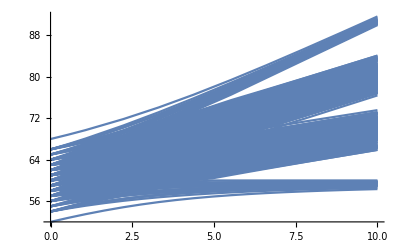

```mathematica
Plot[Sort[Eigenvalues[H[u]]],{u,0,10},PlotPoints->10,MaxRecursion->1]
```

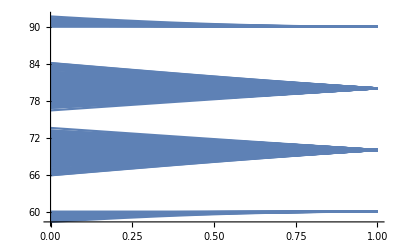

```mathematica
Plot[Sort[Eigenvalues[Hpom[1-t]]],{t,0,1},PlotPoints->10,MaxRecursion->1]
```